## 13 TeV with PDF Monolepton

### Load Parton Level (dσ̂/d Cθ)

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

(* Load dσ/dΩ *)

dσhatdCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-udbar2lpv_X-sec.txt"]]
```

(80698.2 Ein^2 ((-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^4 (0.0816212 x^2 (CHD28til-CHD8til+6 δGF6^2-4 √2 δGF8)-0.461719 δGF6 x+0.65297)^4 (Cθ^2 (4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2+CHud6til^2 x^2+4)+2 Cθ (4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2-CHud6til^2 x^2+4)+4 CHL36til^2 x^2+8 CHL36til x (2 CHQ36til x+1)+4 CHL38til x^2+4 CHQ36til^2 x^2+8 CHQ36til x+4 CHQ38til x^2+CHud6til^2 x^2+4)+4 (Cθ+1)^2 CLQ36til^2 x^2 (6462.07 (0.511403 x^2 (1. CHD28til-1. CHD8til+1.33333 CHL36til^2-3.77124 CHL36til δGF6+1.33333 CHL38til+2.66667 CHQ36til^2-7.54247 CHQ36til δGF6+2.66667 CHQ38til+0.666667 CHud6til^2+8. δGF6^2-5.65685 δGF8)+1.36374 x (1. CHL36til+2. CHQ36til-2.12132 δGF6)+2.04561)^2+16 Ein^4-51696.6 Ein^2+4.17583×10^7)+2 (Cθ+1)^2 (4 Ein^2-6462.07) x (0.0816212 x^2 (CHD28til-CHD8til+6 δGF6^2-4 √2 δGF8)-0.461719 δGF6 x+0.65297)^2 (4 CLQ36til (CHL36til x+CHQ36til x+1) (-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^2+x ((2 CHLQ28til+CHLQ58til) (-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^2-8 CLQs38til Ein^2-4 (Cθ-1) CLQt38til Ein^2))))/((-61.5549 x^2 (δGF6^2-2 √2 δGF8)+174.104 δGF6 x+246.22)^4 (6462.07 (0.511403 x^2 (1. CHD28til-1. CHD8til+1.33333 CHL36til^2-3.77124 CHL36til δGF6+1.33333 CHL38til+2.66667 CHQ36til^2-7.54247 CHQ36til δGF6+2.66667 CHQ38til+0.666667 CHud6til^2+8. δGF6^2-5.65685 δGF8)+1.36374 x (1. CHL36til+2. CHQ36til-2.12132 δGF6)+2.04561)^2+16 Ein^4-51696.6 Ein^2+4.17583×10^7))

### PDF Convolution

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{13.0582,Null}

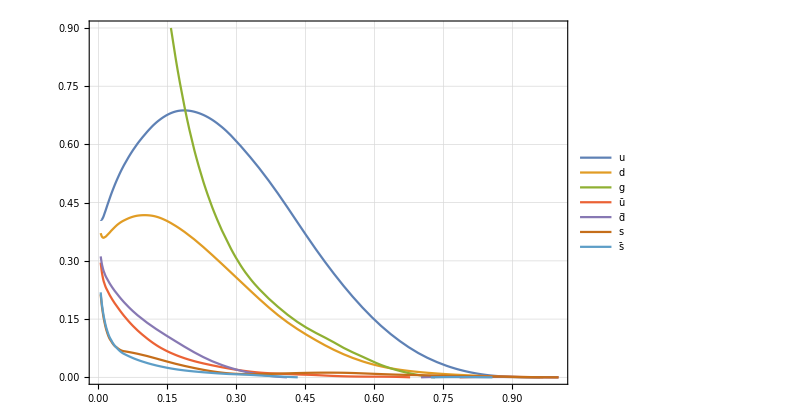

```mathematica
(* Plot xPDF : Peskin pg 563 *)
uppdf=xPDFcv[x,4,2];  (* Peak height is different from the Peskin *)
downpdf=xPDFcv[x,4,1];
gluepdf=xPDFcv[x,4,0];
upbarpdf=xPDFcv[x,4,-2];
dbarpdf=xPDFcv[x,4,-1];
spdf=xPDFcv[x,4,3];
sbarpdf=xPDFcv[x,4,-3];   
Plot[{uppdf,downpdf,gluepdf,upbarpdf,dbarpdf,spdf,sbarpdf},{x,0.005,1},PlotRange->{{0,1},{0,0.9}},PlotLegends->{"u","d","g","ū","d̄","s","s̄"}]
```

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

udbarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 2]);
```

### Proton Level Calculation

#### dσ/dM Calculation

```mathematica
dσdCθwil = dσhatdCθ;
partonicσ[n_]:=Integrate[SeriesCoefficient[dσdCθwil,{x,0,n}],{Cθ,-1,1}]/.Ein->M/2//Simplify
```

```mathematica
variableSM=partonicσ[0];
variableOx=partonicσ[1];
variableOx2=partonicσ[2];
```

```mathematica
(* Assign Wilson Coefficients *)
wilsonCoeflist={};
variablelist=DeleteDuplicates@Cases[variableSM+variableOx+variableOx2,_Symbol,Infinity];
variablelist=DeleteCases[variablelist,M]

For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->3*10^-6]]

σhatwil = variableSM+x variableOx+x^2 variableOx2/.wilsonCoeflist;
σhatSM = variableSM;
```

{CHL36til,CHQ36til,CLQ36til,δGF6,CHD28til,CHD8til,CHL38til,CHQ38til,CHud6til,δGF8,CHLQ28til,CHLQ58til,CLQs38til,CLQt38til}

```mathematica
dσdMSMEFT={};
dσdMSM={};
For[M=1000,M≤5000,M+=10,
(*Print[σhatwil];*)
dσdMSMEFTval=NIntegrate[(σhatwil udbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
dσdMSMval=NIntegrate[(σhatSM udbarpdf)/.x->1, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]}];
AppendTo[dσdMSMEFT,{M,dσdMSMEFTval}];
AppendTo[dσdMSM,{M,dσdMSMval}]
]
Clear[M]
```

```mathematica
dσdMinterpol=Interpolation[dσdMSMEFT];
dσdMSMinterpol=Interpolation[dσdMSM];
```

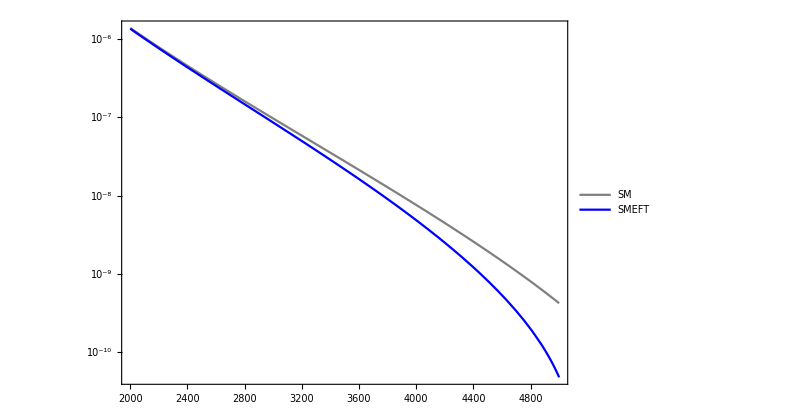

/Users/Tae/Desktop/pp2lnu_SMvsSMEFT.pdf

```mathematica
legend=Placed[LineLegend[{"SM","SMEFT"},LegendFunction->(Framed[#,Background->White]&),LegendMargins->5,LegendLayout->"Column"],{0.9,0.9}];
p1=LogPlot[{dσdMSMinterpol[M],dσdMinterpol[M]},{M,2000,5000},PlotStyle->{Gray,Blue},PlotLegends->legend]
Export["/Users/Tae/Desktop/pp2lnu_SMvsSMEFT.pdf",p1]
```